```mathematica
SetDirectory[ToFileName[("FileName"/.NotebookInformation[EvaluationNotebook[]])[[1]]]];
Clear[Header,FileData12,len,f];f=Import["qk_ca_30.csv"];
FileData12=Take[f,{2,50001}];Header=Take[f,1];Clear[f]; f=Import["test_stat1+2.csv"];FileData13=Take[f,{2,50001}];Clear[f];Header
```

{{N,H1,H0,T1,T2,T3,T4 (max run),T5,T6(0),T8,K[+],K[-],Kdiff,PValue,Evalue,Keys,Error}}

```mathematica
len12 = Length[FileData12];len13 = Length[FileData13];{len12,len13}
```

{50000,50000}

```mathematica
Err1=Select[FileData12,#[[17]]≠0 &]; Pe12=N[Length[Err1]/(len12*20000)];Join[Header, Err1] // MatrixForm
```

(N | H1 | H0 | T1 | T2 | T3 | T4 (max run) | T5 | T6(0) | T8 | K[+] | K[-] | Kdiff | PValue | Evalue | Keys | Error)

```mathematica
Err2=Select[FileData13,#[[17]]≠0 &]; Pe13=N[Length[Err2]/(len13*20000)];Join[Header, Err2] // MatrixForm
```

(N | H1 | H0 | T1 | T2 | T3 | T4 (max run) | T5 | T6(0) | T8 | K[+] | K[-] | Kdiff | PValue | Evalue | Keys | Error)

```mathematica
{Pe12,Pe13}
```

{0.,0.}

```mathematica
{{Min[FileData12[[All,10]]],Max[FileData12[[All,10]]]},{Min[FileData13[[All,10]]],Max[FileData13[[All,10]]]}}//MatrixForm
```

(4.11188 | 4.33974
2.63995 | 2.83897)

```mathematica
{{Min[FileData12[[All,5]]],Max[FileData12[[All,5]]]},{Min[FileData13[[All,5]]],Max[FileData13[[All,5]]]}}//MatrixForm
```

(2.016 | 48.7104
2.3232 | 49.8112)

```mathematica
{{Min[FileData12[[All,2]]],Min[FileData12[[All,3]]]},{Min[FileData13[[All,2]]],Min[FileData13[[All,3]]]}} // MatrixForm
```

(0.999342 | 0.958196
0.999181 | 0.952183)

```mathematica
{{Min[FileData12[[All,14]]],Max[FileData12[[All,14]]]},{Min[FileData13[[All,14]]],Max[FileData13[[All,14]]]}} // MatrixForm
```

(0.33421 | 1.
0.27868 | 1.)

```mathematica
Ent12=Select[FileData12,#[[2]]<0.99913 &];Ent13=Select[FileData13,#[[2]]<0.99913 &];{Length[Ent12],Length[Ent13]}
```

{0,0}

```mathematica
PVal12=Select[FileData12,#[[14]]<0.8&];PVal13=Select[FileData13,#[[14]]<0.8&];{Length[PVal12],Length[PVal13]}
```

{383,350}

```mathematica
K012=Select[FileData12,#[[13]]==0 &];K013=Select[FileData13,#[[13]]==0 &];{Length[K012],Length[K013]}
```

{2694,2565}

```mathematica
{Min[FileData12[[All,14]]],Max[FileData13[[All,14]]]}
```

{0.33421,1.}

```mathematica
P1=Select[FileData12,#[[14]]==1&];Length[P1]
```

1005

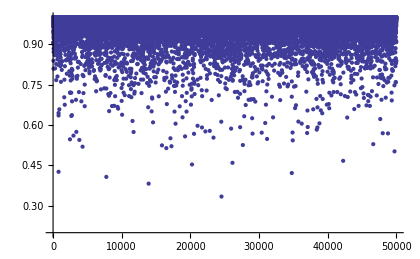
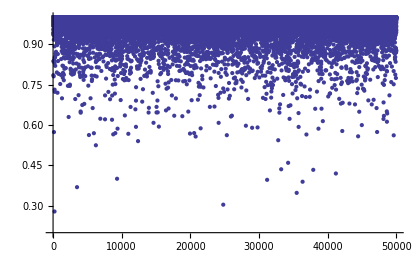
Chi Square Test (P-Value) Cellular Automata rule 30 | Chi Square Test (P-Value) QEKG
-Graphics- | -Graphics-

```mathematica
Grid[{{"Chi Square Test (P-Value) Cellular Automata rule 30","Chi Square Test (P-Value) QEKG"},{ListPlot[FileData12[[All,14]],PlotRange->{0.2,1}, ImageSize->{420,300}],ListPlot[FileData13[[All,14]],PlotRange->{0.2,1},ImageSize->{420,300}]}} ,Frame->All]
```

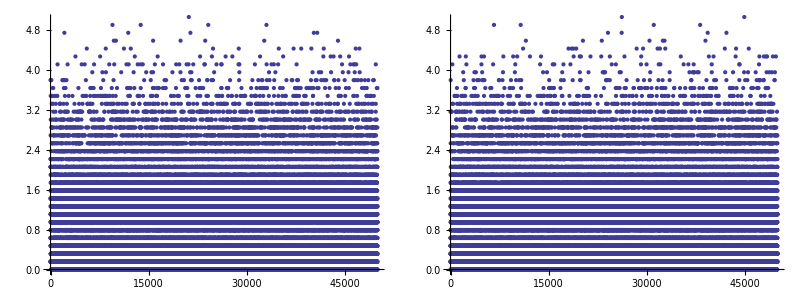

```mathematica
Grid[{{ListPlot[FileData12[[All,13]],PlotRange->{0,5}, ImageSize->{420,300}],ListPlot[FileData13[[All,13]],PlotRange->{0,5},ImageSize->{420,300}]}} ,Frame->All]
```

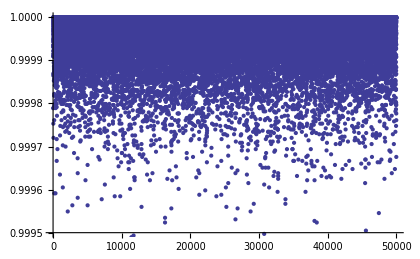
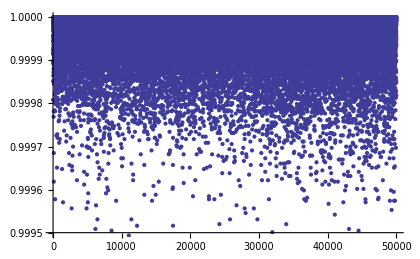
Entropy Cellular Automata rule 30 | Entropy QEKG
-Graphics- | -Graphics-

```mathematica
Grid[{{"Entropy Cellular Automata rule 30","Entropy QEKG"},{ListPlot[FileData12[[All,2]],PlotRange->{0.9995,1}, ImageSize->{420,300}],ListPlot[FileData13[[All,2]],PlotRange->{0.9995,1},ImageSize->{420,300}]}} ,Frame->All]
```

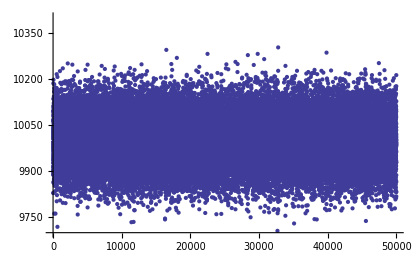
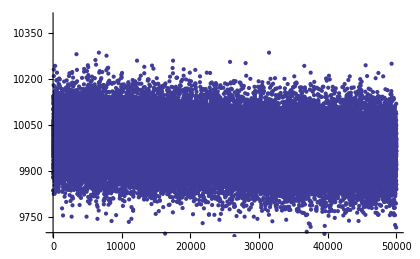
Monobit Test [FI140-1] (T1) Cellular Automata rule 30 | Monobit Test [FI140-1] (T1) QEKG
-Graphics- | -Graphics-

```mathematica
Grid[{{"Monobit Test [FI140-1] (T1) Cellular Automata rule 30", "Monobit Test [FI140-1] (T1) QEKG"},{ListPlot[FileData12[[All,4]],PlotRange->{9700,10400}, ImageSize->{420,300}],ListPlot[FileData13[[All,4]],PlotRange->{9700,10400},ImageSize->{420,300}]}} ,Frame->All]
```

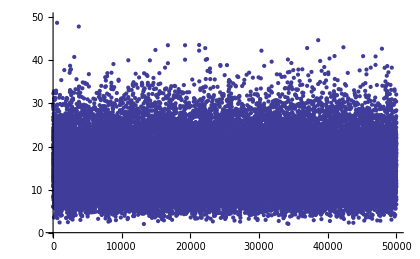
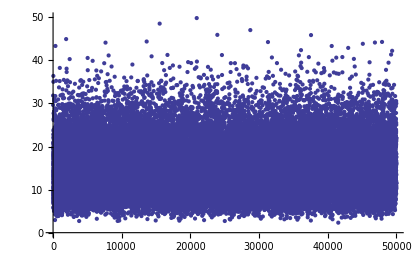
Block Test (T2) Cellular Automata rule 30 | Block Test (T2) QEKG
-Graphics- | -Graphics-

```mathematica
Grid[{{"Block Test (T2) Cellular Automata rule 30", "Block Test (T2) QEKG"},{ListPlot[FileData12[[All,5]],PlotRange->{0,50}, ImageSize->{420,300}],ListPlot[FileData13[[All,5]],PlotRange->{0,50},ImageSize->{420,300}]}} ,Frame->All]
```

```mathematica
Clear[FileData12,FileData13]
```